```mathematica
<<Borsa`
```

```mathematica
If[Directory[]==="C:\\Users\\Joan\\Documents",SetDirectory["C:\\Users\\Joan\\Google Drive\\Borsa\\Ticker\\"],SetDirectory["C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Ticker\\"]];
```

```mathematica
ticker=<<"Ticker"
```

{ABE.MC,ACS.MC,ACX.MC,AENA.MC,AMS.MC,ANA.MC,BBVA.MC,BKIA.MC,BKT.MC,CABK.MC,CLNX.MC,DIA.MC,ELE.MC,ENG.MC,FCC.MC,FER.MC,GAM.MC,GAS.MC,GRF.MC,IAG.MC,IBE.MC,IDR.MC,ITX.MC,MAP.MC,MRL.MC,MTS.MC,POP.MC,REE.MC,REP.MC,SAB.MC,SAN.MC,TEF.MC,TL5.MC,TRE.MC,VIS.MC}

```mathematica
bbva=<<BBVA.MC
```

BBVA.MC
from  Mon 3 Jan 2000  to  Wed 14 Dec 2016
4403  barsStock Object

```mathematica
petit=bbva[{2014,1,1},{2016,12,31}]
```

BBVA.MC
from  Wed 1 Jan 2014  to  Wed 14 Dec 2016
771  barsStock Object

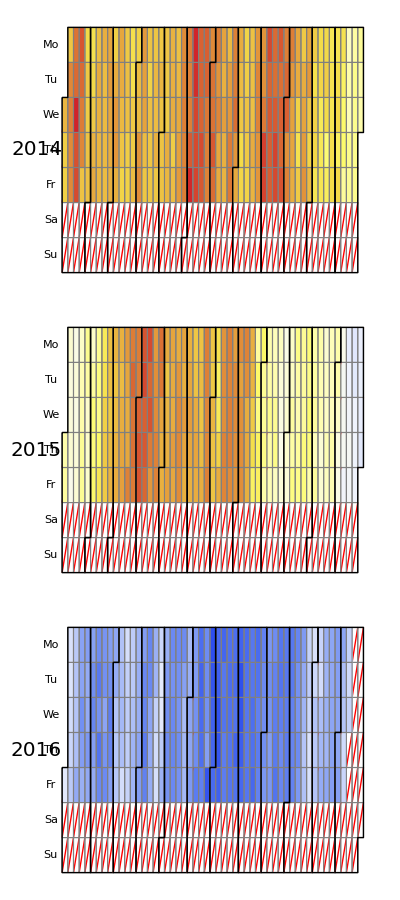

```mathematica
PlotCalendar[TimeSeries[petit["Close"]]]
```

## EMAUpDown

```mathematica
emaUpDown[s_Stock,p_List]:=Module[
{
ema=(Transpose@FinancialIndicator["ExponentialMovingAverage",p[[1]]][s["OHLCV"]]["Path"])[[2]],lows=s["Low"][[All,2]],
closes=s["Close"][[All,2]],
fi, flag=0
},
fi[l_,c_,e_]:=If[l>e &&  flag≠1,flag=1;1,If[c<e && flag==1,flag=-1;-1,0]];
(* Desplaso al dia seguent i retallo el primer per entrar/sortir al dia següent al senyal, elimino els p[[1]] primers pel lag *)Drop[Transpose@{s["Date"][[2;;]],Delete[MapThread[fi,{lows,closes,ema}],-1]},p[[1]]]
]
```

```mathematica
eud=emaUpDown[bbva[{2006,1,1},{2007,12,1}],{20}];
```

```mathematica
eudEntry=#->Column[{"   ↑","Entry"}]&/@(Select[eud,#[[2]]==1&][[All,1]]);
eudExit = #->Placed[Column[{"Exit","  ↓"}],Above]&/@(Select[eud,#[[2]]==-1&][[All,1]]);
eudEE=Join[eudEntry,eudExit];
```

```mathematica
ISTradingChart[bbva[{2006,1,1},{2007,12,1}],{FinancialIndicator["ExponentialMovingAverage",20][bbva["OHLCV"]]["Path"]},EventLabels->eudEE ]
```

```mathematica
zeroLagEMA1[s_Stock,n_Integer]:=
Module[{k=2.0/(n+1),lag=Round[(n-1)/2],price=s["Close"][[All,2]],dates,ema,values},
dates=Drop[s["Close"][[All,1]],n];
ema=FoldList[
((1-k)  #1+k #2)&,price];
values=Drop[
FoldList[
((1-k)  #1+ #2)&,
MapIndexed[If[First[#2]==1,#1,If[First[#2]- lag>0,k (2 #1-ema[[First[#2]- lag]]),k #1]]&,price]
],
n
];
Transpose@{dates,values}
]
```

```mathematica
zeroLagEMA2[s_Stock,n_Integer,g_Real]:=
Module[{k=2.0/(n+1),price=s["Close"][[All,2]],dates,zlema},
dates=Drop[s["Close"][[All,1]],n];
zlema=Drop[FoldList[
((1-k)  #1+k #2+g (#2-#1))&,price]
,n];
Transpose@{dates,zlema}
]
```

```mathematica
zeroLagEMA4[s_Stock,n_Integer,g_Real]:=
Module[{k=2.0/(n+1),price=s["Close"][[All,2]],dates,zlema},
dates=Drop[s["Close"][[All,1]],n];
zlema=Drop[FoldList[
(#1+(g+k-g k)(#2-#1))&,price
],n];
Transpose@{dates,zlema}
]
```

```mathematica
zeroLagEMA3[s_Stock,n_Integer,leastError_:1]:=
Module[
{price=Drop[s["Close"][[All,2]],n],gainLimit=10,
g=0.,zlema},
zlema=zeroLagEMA2[s,n,g];
While[
(Plus@@Abs[100 (zlema[[All,2]]-price)/price]/Length[zlema]>leastError)&& (g≤ gainLimit),
g=g+0.05;
zlema=zeroLagEMA2[s,n,g]
];
Print[g,"   ",Plus@@Abs[100 (zlema[[All,2]]-price)/price]/Length[zlema]];
zlema
]
```

```mathematica
zeroLagEMA5[s_Stock,n_Integer,leastError_:1]:=
Module[
{price=Drop[s["Close"][[All,2]],n],gainLimit=1,
g=0.,zlema},
zlema=zeroLagEMA4[s,n,g];
While[
(Plus@@Abs[100 (zlema[[All,2]]-price)/price]/Length[zlema]>leastError)&& (g≤ gainLimit),
g=g+0.05;
zlema=zeroLagEMA4[s,n,g]
];
Print[g,"   ",Plus@@Abs[100 (zlema[[All,2]]-price)/price]/Length[zlema]];
zlema
]
```

```mathematica
zeroLagEMA3[petit,20,0.01];
```

0.9   0.00914551

```mathematica
petit=bbva[{2016,1,1},{2016,12,1}]
```

BBVA.MC
from  Fri 1 Jan 2016  to  Thu 1 Dec 2016
240  barsStock Object

```mathematica
ISTradingChart[petit,{FinancialIndicator["ExponentialMovingAverage",20][petit["OHLCV"]]["Path"],zeroLagEMA5[petit,20,2]} ]
```

0.25   1.93859

### Slope zeroLagEMA

```mathematica
slopeZLEMA[s_Stock,p_List]:=
Module[{zlEMA,indices,flag},
flag=0;
zlEMA=zeroLagEMA4[s,p[[1]],p[[2]]];
indices=
If[#>0 ,
If[ flag≠1,
flag=1;1,
0
],
If[flag==1,
flag=-1;-1
,0
]
]&/@Differences[zlEMA[[All,2]]];
Transpose@{zlEMA[[3;;,1]],indices[[;;-2]]}
];
```

```mathematica
st=Strategy["slopeZeroLag",{80,0.8}]
```

slopeZeroLag  {80,0.8}
 
 Strategy Object

```mathematica
dom=Flatten[Table[{s,f},{s,30,80,10},{f,0.6,1,0.05}],1]
```

{{30,0.6},{30,0.65},{30,0.7},{30,0.75},{30,0.8},{30,0.85},{30,0.9},{30,0.95},{30,1.},{40,0.6},{40,0.65},{40,0.7},{40,0.75},{40,0.8},{40,0.85},{40,0.9},{40,0.95},{40,1.},{50,0.6},{50,0.65},{50,0.7},{50,0.75},{50,0.8},{50,0.85},{50,0.9},{50,0.95},{50,1.},{60,0.6},{60,0.65},{60,0.7},{60,0.75},{60,0.8},{60,0.85},{60,0.9},{60,0.95},{60,1.},{70,0.6},{70,0.65},{70,0.7},{70,0.75},{70,0.8},{70,0.85},{70,0.9},{70,0.95},{70,1.},{80,0.6},{80,0.65},{80,0.7},{80,0.75},{80,0.8},{80,0.85},{80,0.9},{80,0.95},{80,1.}}

```mathematica
Optimization[bbva,st,dom]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{30,0.6,0.673634},{30,0.65,1.31606},{30,0.7,1.47067},{30,0.75,1.30958},{30,0.8,1.4941},{30,0.85,1.24364},{30,0.9,1.53641},{30,0.95,1.08847},{30,1.,1.18468},{40,0.6,0.713324},{40,0.65,1.4647},{40,0.7,1.2243},{40,0.75,1.44269},{40,0.8,1.5891},{40,0.85,1.53273},{40,0.9,1.56352},{40,0.95,1.09931},{40,1.,1.18165},{50,0.6,0.704537},{50,0.65,1.44898},{50,0.7,1.25799},{50,0.75,1.52336},{50,0.8,1.67896},{50,0.85,1.43129},{50,0.9,1.62778},{50,0.95,1.15194},{50,1.,1.23634},{60,0.6,0.771041},{60,0.65,1.43008},{60,0.7,1.48104},{60,0.75,1.68922},{60,0.8,1.82468},{60,0.85,1.62844},{60,0.9,1.75823},{60,0.95,1.25876},{60,1.,1.34735},{70,0.6,0.695015},{70,0.65,1.28075},{70,0.7,1.42107},{70,0.75,1.574},{70,0.8,1.69975},{70,0.85,1.54135},{70,0.9,1.64067},{70,0.95,1.15886},{70,1.,1.24353},{80,0.6,0.788552},{80,0.65,1.41976},{80,0.7,1.66911},{80,0.75,1.77089},{80,0.8,1.86968},{80,0.85,1.69625},{80,0.9,1.77627},{80,0.95,1.29044},{80,1.,1.34767}}

```mathematica
ListPlot3D[%]
```

-Graphics3D-

```mathematica
bt=BackTest[bbva,st]
```

BBVA.MC  with  slopeZeroLag  {80,0.8}
from  Thu 27 Apr 2000  to  Wed 14 Dec 2016
876  tradesBackTest Object

```mathematica
bt["Performance","Output"->"Table"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Net Return | MDD | Profit Factor | Recovery Factor | Average Trade Return | Winning Trades | Payoff Ratio | Sharpe Ratio | Average Eficiency
1.86968 | 39.2922 | 1.1283 | 1.61108 | 0.00120552 | 0.414857 | 1.59143 | 0.052364 | Indeterminate

```mathematica
bt["Report"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

yeiip_shm27FrontEndObject[LinkObject["yeiip_shm", 3, 1]]27Untitled-5

```mathematica
eud=slopeZLEMA[bbva[{2006,1,1},{2007,12,1}],{80,0.8}];
eudEntry=#->Column[{"   ↑","Entry"}]&/@(Select[eud,#[[2]]==1&][[All,1]]);
eudExit = #->Placed[Column[{"Exit","  ↓"}],Above]&/@(Select[eud,#[[2]]==-1&][[All,1]]);
eudEE=Join[eudEntry,eudExit];
```

```mathematica
ISTradingChart[bbva[{2006,1,1},{2007,1,1}],{zeroLagEMA4[bbva[{2006,1,1},{2007,12,1}],80,0.8]},EventLabels->eudEE ]
```

```mathematica
ISTradingChart[petit,{zeroLagEMA5[petit,100,10],zeroLagEMA5[petit,50,4]} ]
```

0.   6.29816

0.05   3.87388

0.3   1.42787

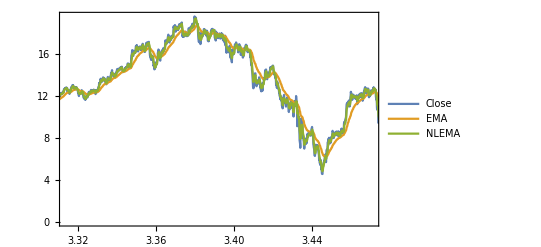

```mathematica
DateListPlot[
{bbva["Close"],
FinancialIndicator["ExponentialMovingAverage",50][bbva["OHLCV"]]["Path"],
zeroLagEMA5[bbva,50,1.5]
},
PlotRange->{{{2005,1,1},{2010,1,1}},All},
PlotLegends->{"Close","EMA","NLEMA"}]
```

### kNN Forecast

```mathematica
petit=bbva[{2014,1,1},{2016,2,1}]
```

BBVA.MC
from  Wed 1 Jan 2014  to  Mon 1 Feb 2016
544  barsStock Object

```mathematica
petit["Properties"]
```

{Name,Date,Open,Close,High,Low,Volume,OHLCV,Median Price,Intraday Range,Interday Range,Dividends,Splits,Adjusted,Weekly Prices,Monthly Prices,Actualize}

```mathematica
?kNNForecast
```

kNNForecast[ts,m,dt,k:1,opts]
	Input: step series, embedding dimension, number of steps to forecast, number of NN
	opts: Weighting->{Mean,Median,Max,Min, ...}, Options[Nearest] 
	Output: step series joined to the dt steps forecasted

```mathematica
m=kNNForecast[petit["Median Price"][[All,2]],30,40,3];
```

```mathematica
h=kNNForecast[petit["High"][[All,2]],30,40,3];
```

```mathematica
l=kNNForecast[petit["Low"][[All,2]],30,40,3];
```

```mathematica
t=(h+l+2*m)/4;
```

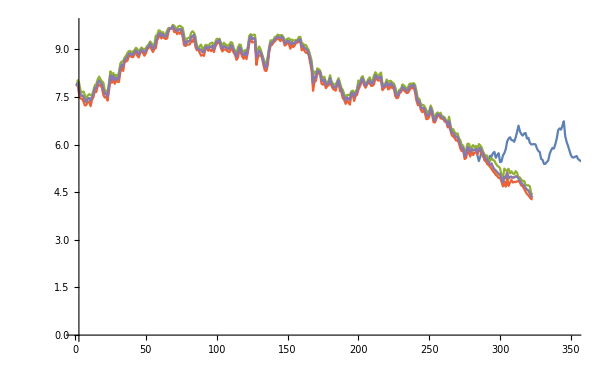

```mathematica
ListLinePlot[{bbva[{2015,1,1},{2017,12,31}]["Median Price"][[All,2]],m,h,l,t},PlotRange->{{1,350},Full}]
```

```mathematica
Options[kNNMA]={"Weighting"->Mean,Options[Nearest]};
```

```mathematica
kNNMA1[s_Stock,m_Integer,dt_Integer,k_Integer:1,opts:OptionsPattern[]]:=
Module[{med,h,l,t},
med=kNNForecast[s["Median Price"][[All,2]],m,dt,k,opts];h=kNNForecast[s["High"][[All,2]],m,dt,k,opts];l=kNNForecast[s["Low"][[All,2]],m,dt,k,opts];t=(h+l+2*med)/4;
{s["Date"][[-1]],(Plus@@s["Median Price"][[-dt-1;;,2]]+Plus@@t[[-dt;;]])/(2 dt+1)}
]
```

```mathematica
kNNMA[s_Stock,m_Integer,dt_Integer,k_Integer:1,opts:OptionsPattern[]]:=
Module[{dmhl,i,prediction={}},
dmhl={s["Date"],s["Median Price"][[All,2]],s["High"][[All,2]],s["Low"][[All,2]]};
For[i=501,i≤Length[s["Date"]],i++,
prediction=Append[prediction,{#[[1]][[-1]],(Plus@@#[[2]][[-dt-1;;]]+Plus@@((kNNForecast[#[[3]],m,dt,k,opts]+kNNForecast[#[[4]],m,dt,k,opts]+2 kNNForecast[#[[2]],m,dt,k,opts])/4)[[-dt;;]])/(2 dt+1)}& [dmhl[[All,;;i]]]];
];
prediction
]
```

```mathematica
pred=kNNMA[bbva,20,20,3];
```

```mathematica
ISTradingChart[bbva,{pred} ]
```

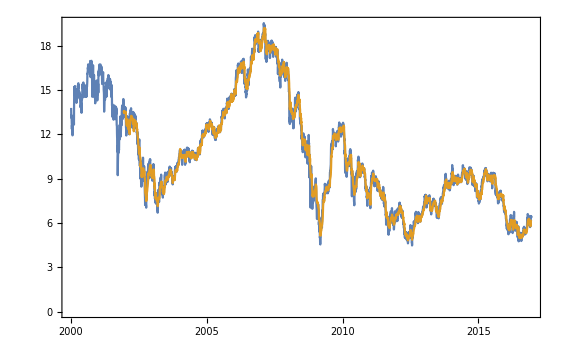

```mathematica
DateListPlot[{bbva["Close"],pred}]
```

```mathematica
Options[kNNSmoth]:={"Weighting"->Mean,Options[Nearest]}
```

```mathematica
kNNSmoth[s_Stock,m_Integer,dt_Integer,k_Integer:1,opts:OptionsPattern[]]:=
Module[
{mp=s["Median Price"],i,prediction={}},
For[i=501,i≤Length[s["Date"]],i++,
prediction=Append[prediction,{#[[-1]][[1]],smoothDCT1[kNNForecast[#[[All,2]],m,dt,k,opts],dt][[-dt-1]]}& [mp[[;;i,All]]]];
];
prediction
]
```

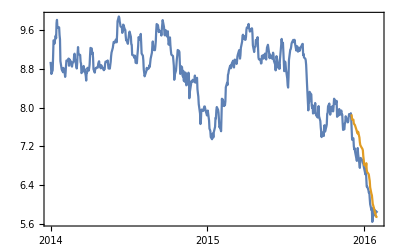

```mathematica
DateListPlot[{petit["Median Price"],kNNSmoth[petit,20,40,3]}]
```

```mathematica
smo=kNNSmoth[bbva,40,40,3];
```

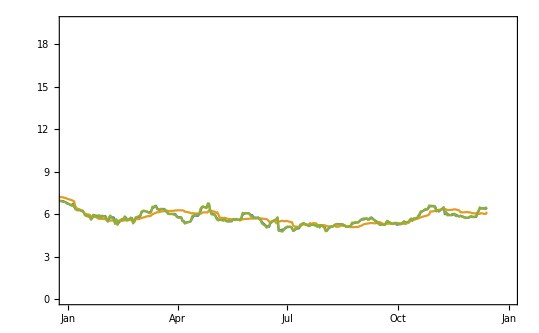

```mathematica
DateListPlot[{bbva["Median Price"],smo,bbva["Close"]},PlotRange->{{{2016,1,1},{2017,1,1}},All}]
```

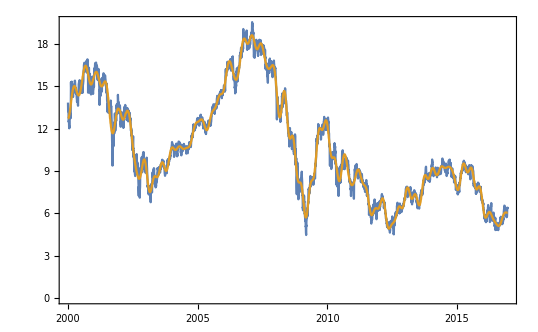

```mathematica
DateListPlot[{bbva["Median Price"],smoothDCT[bbva,40,"Property"-> "Median Price"]}]
```

### knn+zerolag

```mathematica
petit=bbva[{2014,1,1},{2016,2,1}]
```

BBVA.MC
from  Wed 1 Jan 2014  to  Mon 1 Feb 2016
544  barsStock Object

```mathematica
zl=zeroLagEMA4[petit,40,0.5]
```

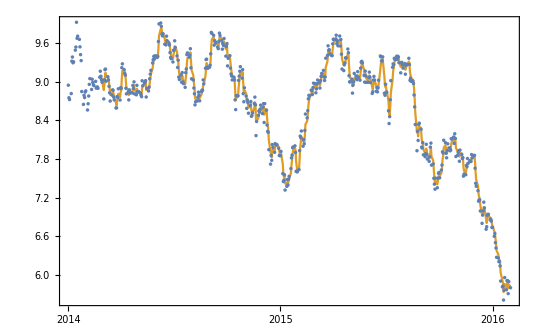

```mathematica
DateListPlot[{petit["Close"],zl},PlotRange->{{{2014,1,1},{2016,2,1}},All},Joined-> {False,True}]
```

```mathematica
?kNNForecast
```

kNNForecast[ts,m,dt,k:1,opts]
	Input: step series, embedding dimension, number of steps to forecast, number of NN
	opts: Weighting->{Mean,Median,Max,Min, ...}, Options[Nearest] 
	Output: step series joined to the dt steps forecasted

```mathematica
zlForecast=kNNForecast[zl[[All,2]],20,20,3];
```

```mathematica
Length[zl]
```

504

```mathematica
dt=30
```

30

```mathematica
fore={};
For[i=301,i<Length[zl]-dt,i++,
fore=Append[fore,kNNForecast[zl[[;;i,2]],20,dt,1][[-1]]];
]
```

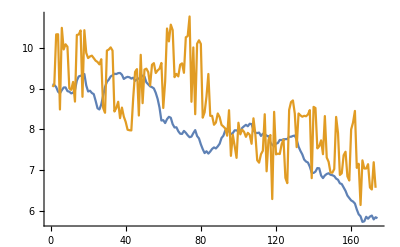

```mathematica
ListLinePlot[{zl[[301+dt;;,2]],fore}]
```

```mathematica
zl=zeroLagEMA4[bbva,40,0.5];
```

```mathematica
Length[zl]
```

4363

```mathematica
dt=1;
```

```mathematica
fore={};
For[i=1001,i≤Length[zl]-dt,i++,
fore=Append[fore,kNNForecast[zl[[;;i,2]],20,dt,1][[-1]]];
]
```

```mathematica
Length/@{zl[[1001+dt;;,2]],fore}
```

{3362,3362}

```mathematica
Median@Abs[zl[[1001+dt;;,2]]-fore]
```

0.104714

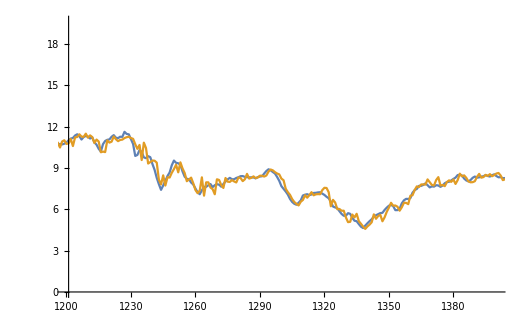

```mathematica
ListLinePlot[{zl[[1001+dt;;,2]],fore},PlotRange->{{1200,1400},All}]
```

```mathematica
DistributeDefinitions[kNNForecast,zl]
```

{kNNForecast,zl}

```mathematica
ParallelEvaluate[Needs["Borsa`","C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Borsa mat\\Workspace\\Borsa\\BorsaV0\\Borsa\\Borsa.m"]]
```

Get::noopen: Cannot open Strategy`.

Needs::nocont: Context Strategy` was not created when Needs was evaluated.

Get::noopen: Cannot open Strategy`.

Needs::nocont: Context Strategy` was not created when Needs was evaluated.

{Null,Null,Null,Null}

```mathematica
ParallelNeeds["C:\\Users\\fabregas.TCMM\\Google Drive\\Borsa\\Borsa mat\\Workspace\\Borsa\\BorsaV0\\Borsa\\Borsa`"]
```

Needs::cxt: Invalid context specified at position 1 in Needs[C:\Users\fabregas.TCMM\Google Drive\Borsa\Borsa mat\Workspace\Borsa\BorsaV0\Borsa\Borsa`]. A context must consist of valid symbol names separated by and ending with `.

```mathematica
Parallelize[
med={};
max={};
For[dt=1,dt≤30,dt=dt+2,
fore={};
For[i=1001,i≤Length[zl]-dt,i++,
fore=Append[fore,kNNForecast[zl[[;;i,2]],20,dt,1][[-1]]];
];
med=Append[med,Median@Abs[zl[[1001+dt;;,2]]-fore]];
max=Append[max,Max@Abs[zl[[1001+dt;;,2]]-fore]];
]
]
```

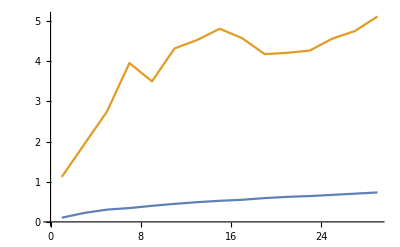

```mathematica
ListLinePlot[{Transpose@{Range[1,30,2],med},Transpose@{Range[1,30,2],max}}]
```

### ssa forecast

```mathematica
phasePortrait3DManipulation[petit["Close"][[All,2]]]
```

```mathematica
X=Transpose@MovingMap[Identity,petit["Close"][[All,2]],499];
```

```mathematica
dmi=distanceMutualInformationH[X[[1]],X[[#]]]&/@Range[1,500];
```

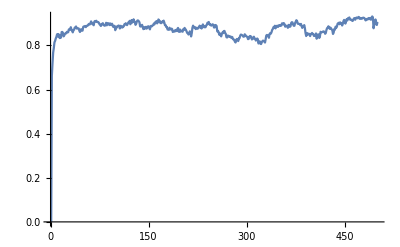

```mathematica
ListLinePlot[dmi]
```

```mathematica
falseNearestNeighbors[petit["Close"][[All,2]],18,10,15,2]
```

{{1,0.685259},{2,0.321088},{3,0.0362622},{4,0.00286123},{5,0.00293686},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.}}

```mathematica
ssa=singularSpectrumAnalysis[petit["Close"][[All,2]],6]
```

{{287145.,57.5219,16.2194,7.77778,5.20052,3.67352},2,{{{8.99961,764,6.38927},5},5}}
 |  |  |  |

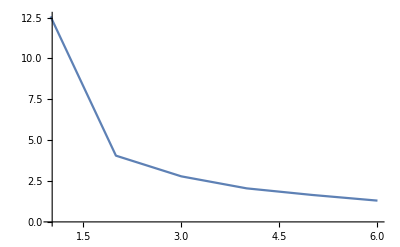

```mathematica
ssaPlotEigenvalues[ssa,6]
```

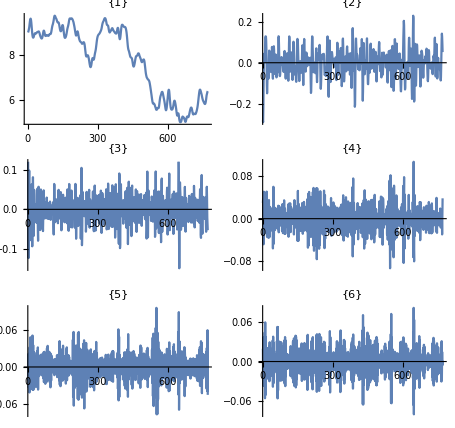

```mathematica
ssaPlotComponents[ssa,6]
```

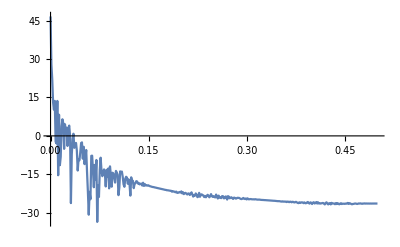

```mathematica
Periodogram[ssa[[2,1]],PlotRange->All]
```

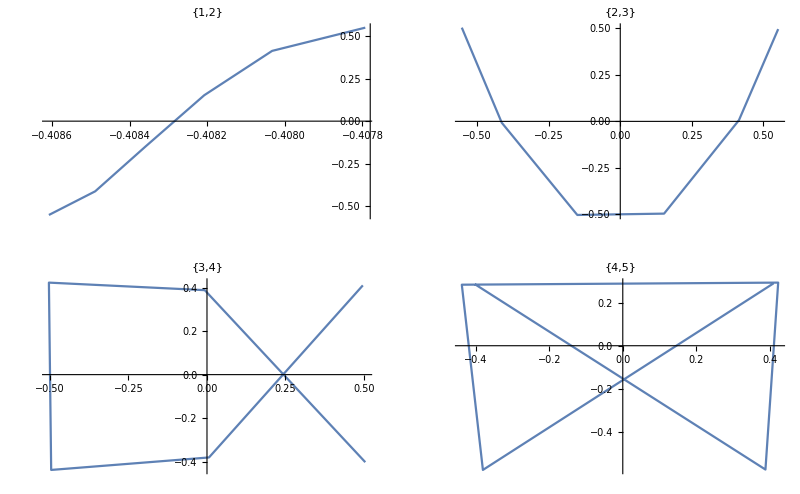

```mathematica
ssaPlotPairVectors[ssa,6]
```

```mathematica
ssawCorrelation[ssa,6]
```

-Graphics-

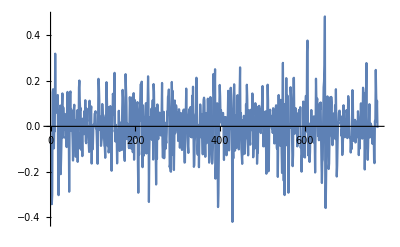

```mathematica
ssaPlotResiduals[ssa,petit["Close"][[All,2]],1]
```

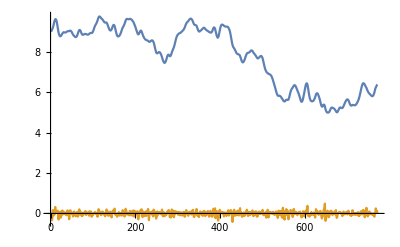

```mathematica
ListLinePlot[{ssaSmoothing[ssa,1],ssaSmoothing[ssa,{2,3,4,5,6}]}]
```

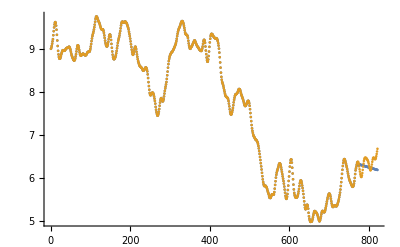

```mathematica
ListPlot[{ssaRForecasting[ssa,1,50],kNNForecast[ssaSmoothing[ssa,1],5,50]}]
```